# Inversor CMOS

```mathematica
nsat = kn(vi-vtn)^2;
ntri = kn(2(vi-vtn)vo - vo^2);
psat = kp(vdd-vi-vtp)^2;
ptri = kp(2(vdd-vi-vtp)(vdd-vo) - (vdd-vo)^2);
```

```mathematica
vm = vi /.Solve[psat == nsat && vi > 0, vi][[1]];
```

```mathematica
vo[vi_]= Piecewise[{{vdd, 0 < vi < vtn}, {vo/.Solve[ptri == nsat,vo][[2]], vtn < vi < vm}, {6, vi == vm}, {vo/.Solve[psat == ntri,vo][[1]], vm < vi < vdd - vtp}, {0, vi > vdd-vtp}}];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
kn = 292.*-6;
kp = 240.*-6;
vdd = 9;
vtn = 1.9;
vtp = 1.7;
```

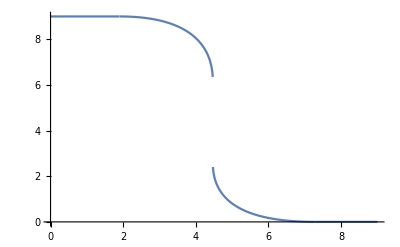

```mathematica
Plot[vo [vi] , {vi,0,vdd}]
```

```mathematica
Quit[]
```